```mathematica
Clear[h]
```

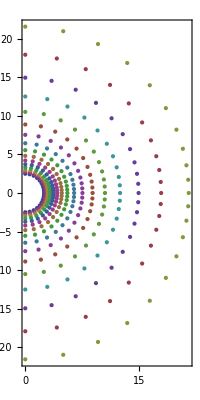

```mathematica
(* metric *)
(* coordinates r,theta grid*)

tKS=x0;
phKS=x3;
rKS=R0+Exp[x1];
thKS=π x2+.5(1-h)Sin[2π x2];
grid=Table[{thKS-π/2,rKS}/.{R0->1.5,h->.5},{x1,0,3,.2},{x2,0,1,.05}];
ListPolarPlot[grid,Frame->True]
```

```mathematica
XKSMKS={{D[tKS,x0],D[tKS,x1],D[tKS,x2],D[tKS,x3]},
{D[rKS,x0],D[rKS,x1],D[rKS,x2],D[rKS,x3]},
{D[thKS,x0],D[thKS,x1],D[thKS,x2],D[thKS,x3]},
{D[phKS,x0],D[phKS,x1],D[phKS,x2],D[phKS,x3]}};
```

```mathematica
TableForm[XKSMKS]
```

1 | 0 | 0 | 0
0 | ⅇ^x1 | 0 | 0
0 | 0 | π+3.14159 (1-h) Cos[2 π x2] | 0
0 | 0 | 0 | 1

```mathematica
(* spherical g_munu (-+++) *)
scoor = {r->x1,θ->x2, ϕ->x3};
Σ=r^2+a^2 Cos[θ]^2;
Δ=r^2-2r+a^2;
A=(r^2+a^2)^2-a^2 Δ Sin[θ]^2
g00=-(1-(2r)/Σ);
g03=g30=-(2r)/Σ a Sin[θ]^2;
g11=1+2 r/Σ;
g22=Σ;
g33=Sin[θ]^2(Σ+a^2(1+(2r)/Σ)Sin[θ]^2);
g01=g10=(2r)/Σ;
g13=g31=-a(1+(2r)/Σ)Sin[θ]^2;
g02=g12=g20=g21=g23=g32=0;
```

(a^2+r^2)^2-a^2 (a^2-2 r+r^2) Sin[θ]^2

```mathematica
(* matrix form *)
g=Simplify[{{g00,g01,g02,g03},{g10,g11,g12,g13},{g20,g21,g22,g23},{g30,g31,g32,g33}}];
g=g/.scoor;
MatrixForm[g]
```

(-1+(2 x1)/(x1^2+a^2 Cos[x2]^2) | (2 x1)/(x1^2+a^2 Cos[x2]^2) | 0 | -(2 a x1 Sin[x2]^2)/(x1^2+a^2 Cos[x2]^2)
(2 x1)/(x1^2+a^2 Cos[x2]^2) | 1+(2 x1)/(x1^2+a^2 Cos[x2]^2) | 0 | -a (1+(2 x1)/(x1^2+a^2 Cos[x2]^2)) Sin[x2]^2
0 | 0 | x1^2+a^2 Cos[x2]^2 | 0
-(2 a x1 Sin[x2]^2)/(x1^2+a^2 Cos[x2]^2) | -a (1+(2 x1)/(x1^2+a^2 Cos[x2]^2)) Sin[x2]^2 | 0 | Sin[x2]^2 (x1^2+a^2 Cos[x2]^2+a^2 (1+(2 x1)/(x1^2+a^2 Cos[x2]^2)) Sin[x2]^2))

```mathematica
(* a=0 *)
MatrixForm[g/.scoor/.{a->0}]
```

(-1+2/x1 | 2/x1 | 0 | 0
2/x1 | 1+2/x1 | 0 | 0
0 | 0 | x1^2 | 0
0 | 0 | 0 | x1^2 Sin[x2]^2)

```mathematica
(* inversed metric g^munu *)
MatrixForm[G=Simplify[Inverse[g]]]
G00=G[[1,1]];G01=G[[1,2]];G02=G[[1,3]];G03=G[[1,4]];
G10=G[[2,1]];G11=G[[2,2]];G12=G[[2,3]];G13=G[[2,4]];
G20=G[[3,1]];G21=G[[3,2]];G22=G[[3,3]];G23=G[[3,4]];
G30=G[[4,1]];G31=G[[4,2]];G32=G[[4,3]];
G33=G[[4,4]];
```

(-(x1 (2+x1)+a^2 Cos[x2]^2)/(x1^2+a^2 Cos[x2]^2) | (2 x1)/(x1^2+a^2 Cos[x2]^2) | 0 | 0
(2 x1)/(x1^2+a^2 Cos[x2]^2) | (a^2+(-2+x1) x1)/(x1^2+a^2 Cos[x2]^2) | 0 | a/(x1^2+a^2 Cos[x2]^2)
0 | 0 | 1/(x1^2+a^2 Cos[x2]^2) | 0
0 | a/(x1^2+a^2 Cos[x2]^2) | 0 | Csc[x2]^2/(x1^2+a^2 Cos[x2]^2))

```mathematica
(* matrix determinant *)
gdet=Simplify[Sqrt[-Det[g]]]
```

√((x1^2+a^2 Cos[x2]^2)^2 Sin[x2]^2)

```mathematica
(*matrix determinant log derivatives*)
dlgdet=Simplify[{D[gdet,x1]/gdet,D[gdet,x2]/gdet,D[gdet,x3]/gdet}]
```

{(2 x1)/(x1^2+a^2 Cos[x2]^2),((-a^2+2 x1^2+3 a^2 Cos[2 x2]) Cot[x2])/(2 (x1^2+a^2 Cos[x2]^2)),0}

```mathematica
(* auxiliary matrices of derivatives *)
dgdx = {D[g,x0],D[g,x1],D[g,x2],D[g,x3]}
```

{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{-(4 x1^2)/((x1^2+a^2 Cos[x2]^2)^2)+2/(x1^2+a^2 Cos[x2]^2),-(4 x1^2)/((x1^2+a^2 Cos[x2]^2)^2)+2/(x1^2+a^2 Cos[x2]^2),0,(4 a x1^2 Sin[x2]^2)/((x1^2+a^2 Cos[x2]^2)^2)-(2 a Sin[x2]^2)/(x1^2+a^2 Cos[x2]^2)},{-(4 x1^2)/((x1^2+a^2 Cos[x2]^2)^2)+2/(x1^2+a^2 Cos[x2]^2),-(4 x1^2)/((x1^2+a^2 Cos[x2]^2)^2)+2/(x1^2+a^2 Cos[x2]^2),0,-a (-(4 x1^2)/((x1^2+a^2 Cos[x2]^2)^2)+2/(x1^2+a^2 Cos[x2]^2)) Sin[x2]^2},{0,0,2 x1,0},{(4 a x1^2 Sin[x2]^2)/((x1^2+a^2 Cos[x2]^2)^2)-(2 a Sin[x2]^2)/(x1^2+a^2 Cos[x2]^2),-a (-(4 x1^2)/((x1^2+a^2 Cos[x2]^2)^2)+2/(x1^2+a^2 Cos[x2]^2)) Sin[x2]^2,0,Sin[x2]^2 (2 x1+a^2 (-(4 x1^2)/((x1^2+a^2 Cos[x2]^2)^2)+2/(x1^2+a^2 Cos[x2]^2)) Sin[x2]^2)}},{{(4 a^2 x1 Cos[x2] Sin[x2])/((x1^2+a^2 Cos[x2]^2)^2),(4 a^2 x1 Cos[x2] Sin[x2])/((x1^2+a^2 Cos[x2]^2)^2),0,-(4 a x1 Cos[x2] Sin[x2])/(x1^2+a^2 Cos[x2]^2)-(4 a^3 x1 Cos[x2] Sin[x2]^3)/((x1^2+a^2 Cos[x2]^2)^2)},{(4 a^2 x1 Cos[x2] Sin[x2])/((x1^2+a^2 Cos[x2]^2)^2),(4 a^2 x1 Cos[x2] Sin[x2])/((x1^2+a^2 Cos[x2]^2)^2),0,-2 a Cos[x2] (1+(2 x1)/(x1^2+a^2 Cos[x2]^2)) Sin[x2]-(4 a^3 x1 Cos[x2] Sin[x2]^3)/((x1^2+a^2 Cos[x2]^2)^2)},{0,0,-2 a^2 Cos[x2] Sin[x2],0},{-(4 a x1 Cos[x2] Sin[x2])/(x1^2+a^2 Cos[x2]^2)-(4 a^3 x1 Cos[x2] Sin[x2]^3)/((x1^2+a^2 Cos[x2]^2)^2),-2 a Cos[x2] (1+(2 x1)/(x1^2+a^2 Cos[x2]^2)) Sin[x2]-(4 a^3 x1 Cos[x2] Sin[x2]^3)/((x1^2+a^2 Cos[x2]^2)^2),0,2 Cos[x2] Sin[x2] (x1^2+a^2 Cos[x2]^2+a^2 (1+(2 x1)/(x1^2+a^2 Cos[x2]^2)) Sin[x2]^2)+Sin[x2]^2 (-2 a^2 Cos[x2] Sin[x2]+2 a^2 Cos[x2] (1+(2 x1)/(x1^2+a^2 Cos[x2]^2)) Sin[x2]+(4 a^4 x1 Cos[x2] Sin[x2]^3)/((x1^2+a^2 Cos[x2]^2)^2))}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
(* Christofells with 3 lower indices *)
γ=Table[(dgdx[[k,i,j]]+dgdx[[j,i,k]]-dgdx[[i,j,k]])/2,{i,1,4},{j,1,4},{k,1,4}];
```

```mathematica
(* Christofells with 1st index up *)
Γ=Simplify[Table[Sum[G[[i,b]]γ[[b,j,k]],{b,1,4}],{i,1,4},{j,1,4},{k,1,4}]]
```

{{{(2 x1 (x1^2-a^2 Cos[x2]^2))/((x1^2+a^2 Cos[x2]^2)^3),((x1^2-a^2 Cos[x2]^2) (x1 (2+x1)+a^2 Cos[x2]^2))/((x1^2+a^2 Cos[x2]^2)^3),-(2 a^2 x1 Cos[x2] Sin[x2])/((x1^2+a^2 Cos[x2]^2)^2),(2 a x1 (-x1^2+a^2 Cos[x2]^2) Sin[x2]^2)/((x1^2+a^2 Cos[x2]^2)^3)},{((x1^2-a^2 Cos[x2]^2) (x1 (2+x1)+a^2 Cos[x2]^2))/((x1^2+a^2 Cos[x2]^2)^3),(2 (x1^2-a^2 Cos[x2]^2) (x1+x1^2+a^2 Cos[x2]^2))/((x1^2+a^2 Cos[x2]^2)^3),-(2 a^2 x1 Cos[x2] Sin[x2])/((x1^2+a^2 Cos[x2]^2)^2),(a (-x1^2+a^2 Cos[x2]^2) (x1 (2+x1)+a^2 Cos[x2]^2) Sin[x2]^2)/((x1^2+a^2 Cos[x2]^2)^3)},{-(2 a^2 x1 Cos[x2] Sin[x2])/((x1^2+a^2 Cos[x2]^2)^2),-(2 a^2 x1 Cos[x2] Sin[x2])/((x1^2+a^2 Cos[x2]^2)^2),-(2 x1^2)/(x1^2+a^2 Cos[x2]^2),(2 a^3 x1 Cos[x2] Sin[x2]^3)/((x1^2+a^2 Cos[x2]^2)^2)},{(2 a x1 (-x1^2+a^2 Cos[x2]^2) Sin[x2]^2)/((x1^2+a^2 Cos[x2]^2)^3),(a (-x1^2+a^2 Cos[x2]^2) (x1 (2+x1)+a^2 Cos[x2]^2) Sin[x2]^2)/((x1^2+a^2 Cos[x2]^2)^3),(2 a^3 x1 Cos[x2] Sin[x2]^3)/((x1^2+a^2 Cos[x2]^2)^2),-(2 x1 Sin[x2]^2 (x1^5+a^4 x1 Cos[x2]^4-a^2 x1^2 Sin[x2]^2+Cos[x2]^2 (2 a^2 x1^3+a^4 Sin[x2]^2)))/((x1^2+a^2 Cos[x2]^2)^3)}},{{-((a^2+(-2+x1) x1) (-x1^2+a^2 Cos[x2]^2))/((x1^2+a^2 Cos[x2]^2)^3),-((x1^2-a^2 Cos[x2]^2) (2 x1-a^2 Sin[x2]^2))/((x1^2+a^2 Cos[x2]^2)^3),0,(a (a^2+(-2+x1) x1) (-x1^2+a^2 Cos[x2]^2) Sin[x2]^2)/((x1^2+a^2 Cos[x2]^2)^3)},{-((x1^2-a^2 Cos[x2]^2) (2 x1-a^2 Sin[x2]^2))/((x1^2+a^2 Cos[x2]^2)^3),-((x1^2-a^2 Cos[x2]^2) (x1 (2+x1)+a^2 Cos[2 x2]))/((x1^2+a^2 Cos[x2]^2)^3),-(a^2 Sin[2 x2])/(a^2+2 x1^2+a^2 Cos[2 x2]),(a Sin[x2]^2 (a^4 x1 Cos[x2]^4+x1^2 (2 x1+x1^3-a^2 Sin[x2]^2)+a^2 Cos[x2]^2 (2 x1 (-1+x1^2)+a^2 Sin[x2]^2)))/((x1^2+a^2 Cos[x2]^2)^3)},{0,-(a^2 Sin[2 x2])/(a^2+2 x1^2+a^2 Cos[2 x2]),-(x1 (a^2+(-2+x1) x1))/(x1^2+a^2 Cos[x2]^2),0},{(a (a^2+(-2+x1) x1) (-x1^2+a^2 Cos[x2]^2) Sin[x2]^2)/((x1^2+a^2 Cos[x2]^2)^3),(a Sin[x2]^2 (a^4 x1 Cos[x2]^4+x1^2 (2 x1+x1^3-a^2 Sin[x2]^2)+a^2 Cos[x2]^2 (2 x1 (-1+x1^2)+a^2 Sin[x2]^2)))/((x1^2+a^2 Cos[x2]^2)^3),0,-((a^2+(-2+x1) x1) Sin[x2]^2 (x1^5+a^4 x1 Cos[x2]^4-a^2 x1^2 Sin[x2]^2+Cos[x2]^2 (2 a^2 x1^3+a^4 Sin[x2]^2)))/((x1^2+a^2 Cos[x2]^2)^3)}},{{-(2 a^2 x1 Cos[x2] Sin[x2])/((x1^2+a^2 Cos[x2]^2)^3),-(2 a^2 x1 Cos[x2] Sin[x2])/((x1^2+a^2 Cos[x2]^2)^3),0,(a x1 (a^2+x1^2) Sin[2 x2])/((x1^2+a^2 Cos[x2]^2)^3)},{-(2 a^2 x1 Cos[x2] Sin[x2])/((x1^2+a^2 Cos[x2]^2)^3),-(2 a^2 x1 Cos[x2] Sin[x2])/((x1^2+a^2 Cos[x2]^2)^3),x1/(x1^2+a^2 Cos[x2]^2),(a Cos[x2] Sin[x2] (x1^3 (2+x1)+2 a^2 x1 (1+x1) Cos[x2]^2+a^4 Cos[x2]^4+2 a^2 x1 Sin[x2]^2))/((x1^2+a^2 Cos[x2]^2)^3)},{0,x1/(x1^2+a^2 Cos[x2]^2),-(a^2 Cos[x2] Sin[x2])/(x1^2+a^2 Cos[x2]^2),0},{(a x1 (a^2+x1^2) Sin[2 x2])/((x1^2+a^2 Cos[x2]^2)^3),(a Cos[x2] Sin[x2] (x1^3 (2+x1)+2 a^2 x1 (1+x1) Cos[x2]^2+a^4 Cos[x2]^4+2 a^2 x1 Sin[x2]^2))/((x1^2+a^2 Cos[x2]^2)^3),0,-1/((x1^2+a^2 Cos[x2]^2)^3)Cos[x2] Sin[x2] (a^6 Cos[x2]^6+Cos[x2]^4 (3 a^4 x1^2+a^6 Sin[x2]^2)+Cos[x2]^2 (3 a^2 x1^4+2 a^4 x1^2 Sin[x2]^2)+x1 (x1^5+a^2 x1^2 (4+x1) Sin[x2]^2+2 a^4 Sin[x2]^4+a^4 Sin[2 x2]^2))}},{{(a x1^2-a^3 Cos[x2]^2)/((x1^2+a^2 Cos[x2]^2)^3),(a (x1^2-a^2 Cos[x2]^2))/((x1^2+a^2 Cos[x2]^2)^3),-(2 a x1 Cot[x2])/((x1^2+a^2 Cos[x2]^2)^2),(a^2 (-x1^2+a^2 Cos[x2]^2) Sin[x2]^2)/((x1^2+a^2 Cos[x2]^2)^3)},{(a (x1^2-a^2 Cos[x2]^2))/((x1^2+a^2 Cos[x2]^2)^3),(a x1^2-a^3 Cos[x2]^2)/((x1^2+a^2 Cos[x2]^2)^3),-(a (x1 (2+x1)+a^2 Cos[x2]^2) Cot[x2])/((x1^2+a^2 Cos[x2]^2)^2),(x1^5+a^4 x1 Cos[x2]^4-a^2 x1^2 Sin[x2]^2+Cos[x2]^2 (2 a^2 x1^3+a^4 Sin[x2]^2))/((x1^2+a^2 Cos[x2]^2)^3)},{-(2 a x1 Cot[x2])/((x1^2+a^2 Cos[x2]^2)^2),-(a (x1 (2+x1)+a^2 Cos[x2]^2) Cot[x2])/((x1^2+a^2 Cos[x2]^2)^2),-(a x1)/(x1^2+a^2 Cos[x2]^2),(1/4 (a^2+2 x1^2+a^2 Cos[2 x2])^2 Cot[x2]+a^2 x1 Sin[2 x2])/((x1^2+a^2 Cos[x2]^2)^2)},{(a^2 (-x1^2+a^2 Cos[x2]^2) Sin[x2]^2)/((x1^2+a^2 Cos[x2]^2)^3),(x1^5+a^4 x1 Cos[x2]^4-a^2 x1^2 Sin[x2]^2+Cos[x2]^2 (2 a^2 x1^3+a^4 Sin[x2]^2))/((x1^2+a^2 Cos[x2]^2)^3),(1/4 (a^2+2 x1^2+a^2 Cos[2 x2])^2 Cot[x2]+a^2 x1 Sin[2 x2])/((x1^2+a^2 Cos[x2]^2)^2),-(a Sin[x2]^2 (x1^5+a^4 x1 Cos[x2]^4-a^2 x1^2 Sin[x2]^2+Cos[x2]^2 (2 a^2 x1^3+a^4 Sin[x2]^2)))/((x1^2+a^2 Cos[x2]^2)^3)}}}

```mathematica
(* determinant in CForm *)
CForm[gdet]
```

Sqrt(Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),2)*
    Power(Sin(x2),2))

```mathematica
(* dlog determinant in CForm *)
TableForm[{
";if(idim==0) return " CForm[dlgdet[[1]]],
";if(idim==1) return " CForm[dlgdet[[2]]],
";if(idim==2) return " CForm[dlgdet[[3]]],";"}]
```

;if(idim==0) return  (2*x1)/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2))
;if(idim==1) return  ((-Power(a,2) + 2*Power(x1,2) + 3*Power(a,2)*Cos(2*x2))*Cot(x2))/(2.*(Power(x1,2) + Power(a,2)*Power(Cos(x2),2)))
;if(idim==2) return  0
;

```mathematica
(* metric in CForm *)
gC=TableForm[{
";g[0][0]="CForm[g[[1,1]]],
";g[0][1]="CForm[g[[1,2]]],
";g[0][2]="CForm[g[[1,3]]],
";g[0][3]="CForm[g[[1,4]]],
";g[1][0]="CForm[g[[2,1]]],
";g[1][1]="CForm[g[[2,2]]],
";g[1][2]="CForm[g[[2,3]]],
";g[1][3]="CForm[g[[2,4]]],
";g[2][0]="CForm[g[[3,1]]],
";g[2][1]="CForm[g[[3,2]]],
";g[2][2]="CForm[g[[3,3]]],
";g[2][3]="CForm[g[[3,4]]],
";g[3][0]="CForm[g[[4,1]]],
";g[3][1]="CForm[g[[4,2]]],
";g[3][2]="CForm[g[[4,3]]],
";g[3][3]="CForm[g[[4,4]]],";"
}]
```

;g[0][0]= -1 + (2*x1)/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2))
;g[0][1]= (2*x1)/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2))
;g[0][2]= 0
;g[0][3]= (-2*a*x1*Power(Sin(x2),2))/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2))
;g[1][0]= (2*x1)/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2))
;g[1][1]= 1 + (2*x1)/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2))
;g[1][2]= 0
;g[1][3]= -(a*(1 + (2*x1)/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2)))*Power(Sin(x2),2))
;g[2][0]= 0
;g[2][1]= 0
;g[2][2]= Power(x1,2) + Power(a,2)*Power(Cos(x2),2)
;g[2][3]= 0
;g[3][0]= (-2*a*x1*Power(Sin(x2),2))/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2))
;g[3][1]= -(a*(1 + (2*x1)/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2)))*Power(Sin(x2),2))
;g[3][2]= 0
;g[3][3]= Power(Sin(x2),2)*(Power(x1,2) + Power(a,2)*Power(Cos(x2),2) + Power(a,2)*(1 + (2*x1)/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2)))*Power(Sin(x2),2))
;

```mathematica
(* inversed metric in CForm *)
GC=TableForm[{
";G[0][0]="CForm[G[[1,1]]],
";G[0][1]="CForm[G[[1,2]]],
";G[0][2]="CForm[G[[1,3]]],
";G[0][3]="CForm[G[[1,4]]],
";G[1][0]="CForm[G[[2,1]]],
";G[1][1]="CForm[G[[2,2]]],
";G[1][2]="CForm[G[[2,3]]],
";G[1][3]="CForm[G[[2,4]]],
";G[2][0]="CForm[G[[3,1]]],
";G[2][1]="CForm[G[[3,2]]],
";G[2][2]="CForm[G[[3,3]]],
";G[2][3]="CForm[G[[3,4]]],
";G[3][0]="CForm[G[[4,1]]],
";G[3][1]="CForm[G[[4,2]]],
";G[3][2]="CForm[G[[4,3]]],
";G[3][3]="CForm[G[[4,4]]],";"
}]
```

;G[0][0]= -((x1*(2 + x1) + Power(a,2)*Power(Cos(x2),2))/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2)))
;G[0][1]= (2*x1)/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2))
;G[0][2]= 0
;G[0][3]= 0
;G[1][0]= (2*x1)/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2))
;G[1][1]= (Power(a,2) + (-2 + x1)*x1)/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2))
;G[1][2]= 0
;G[1][3]= a/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2))
;G[2][0]= 0
;G[2][1]= 0
;G[2][2]= 1/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2))
;G[2][3]= 0
;G[3][0]= 0
;G[3][1]= a/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2))
;G[3][2]= 0
;G[3][3]= Power(Csc(x2),2)/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2))
;

```mathematica
(* Christoffels in CForm *)
ΓC=TableForm[{
";Krzys[0][0][0]="CForm[Γ[[1,1,1]]],
";Krzys[0][0][1]="CForm[Γ[[1,1,2]]],
";Krzys[0][0][2]="CForm[Γ[[1,1,3]]],
";Krzys[0][0][3]="CForm[Γ[[1,1,4]]],
";Krzys[0][1][0]="CForm[Γ[[1,2,1]]],
";Krzys[0][1][1]="CForm[Γ[[1,2,2]]],
";Krzys[0][1][2]="CForm[Γ[[1,2,3]]],
";Krzys[0][1][3]="CForm[Γ[[1,2,4]]],
";Krzys[0][2][0]="CForm[Γ[[1,3,1]]],
";Krzys[0][2][1]="CForm[Γ[[1,3,2]]],
";Krzys[0][2][2]="CForm[Γ[[1,3,3]]],
";Krzys[0][2][3]="CForm[Γ[[1,3,4]]],
";Krzys[0][3][0]="CForm[Γ[[1,4,1]]],
";Krzys[0][3][1]="CForm[Γ[[1,4,2]]],
";Krzys[0][3][2]="CForm[Γ[[1,4,3]]],
";Krzys[0][3][3]="CForm[Γ[[1,4,4]]],

";Krzys[1][0][0]="CForm[Γ[[2,1,1]]],
";Krzys[1][0][1]="CForm[Γ[[2,1,2]]],
";Krzys[1][0][2]="CForm[Γ[[2,1,3]]],
";Krzys[1][0][3]="CForm[Γ[[2,1,4]]],
";Krzys[1][1][0]="CForm[Γ[[2,2,1]]],
";Krzys[1][1][1]="CForm[Γ[[2,2,2]]],
";Krzys[1][1][2]="CForm[Γ[[2,2,3]]],
";Krzys[1][1][3]="CForm[Γ[[2,2,4]]],
";Krzys[1][2][0]="CForm[Γ[[2,3,1]]],
";Krzys[1][2][1]="CForm[Γ[[2,3,2]]],
";Krzys[1][2][2]="CForm[Γ[[2,3,3]]],
";Krzys[1][2][3]="CForm[Γ[[2,3,4]]],
";Krzys[1][3][0]="CForm[Γ[[2,4,1]]],
";Krzys[1][3][1]="CForm[Γ[[2,4,2]]],
";Krzys[1][3][2]="CForm[Γ[[2,4,3]]],
";Krzys[1][3][3]="CForm[Γ[[2,4,4]]],

";Krzys[2][0][0]="CForm[Γ[[3,1,1]]],
";Krzys[2][0][1]="CForm[Γ[[3,1,2]]],
";Krzys[2][0][2]="CForm[Γ[[3,1,3]]],
";Krzys[2][0][3]="CForm[Γ[[3,1,4]]],
";Krzys[2][1][0]="CForm[Γ[[3,2,1]]],
";Krzys[2][1][1]="CForm[Γ[[3,2,2]]],
";Krzys[2][1][2]="CForm[Γ[[3,2,3]]],
";Krzys[2][1][3]="CForm[Γ[[3,2,4]]],
";Krzys[2][2][0]="CForm[Γ[[3,3,1]]],
";Krzys[2][2][1]="CForm[Γ[[3,3,2]]],
";Krzys[2][2][2]="CForm[Γ[[3,3,3]]],
";Krzys[2][2][3]="CForm[Γ[[3,3,4]]],
";Krzys[2][3][0]="CForm[Γ[[3,4,1]]],
";Krzys[2][3][1]="CForm[Γ[[3,4,2]]],
";Krzys[2][3][2]="CForm[Γ[[3,4,3]]],
";Krzys[2][3][3]="CForm[Γ[[3,4,4]]],

";Krzys[3][0][0]="CForm[Γ[[4,1,1]]],
";Krzys[3][0][1]="CForm[Γ[[4,1,2]]],
";Krzys[3][0][2]="CForm[Γ[[4,1,3]]],
";Krzys[3][0][3]="CForm[Γ[[4,1,4]]],
";Krzys[3][1][0]="CForm[Γ[[4,2,1]]],
";Krzys[3][1][1]="CForm[Γ[[4,2,2]]],
";Krzys[3][1][2]="CForm[Γ[[4,2,3]]],
";Krzys[3][1][3]="CForm[Γ[[4,2,4]]],
";Krzys[3][2][0]="CForm[Γ[[4,3,1]]],
";Krzys[3][2][1]="CForm[Γ[[4,3,2]]],
";Krzys[3][2][2]="CForm[Γ[[4,3,3]]],
";Krzys[3][2][3]="CForm[Γ[[4,3,4]]],
";Krzys[3][3][0]="CForm[Γ[[4,4,1]]],
";Krzys[3][3][1]="CForm[Γ[[4,4,2]]],
";Krzys[3][3][2]="CForm[Γ[[4,4,3]]],
";Krzys[3][3][3]="CForm[Γ[[4,4,4]]],
";"
}]
```

;Krzys[0][0][0]= (2*x1*(Power(x1,2) - Power(a,2)*Power(Cos(x2),2)))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[0][0][1]= ((Power(x1,2) - Power(a,2)*Power(Cos(x2),2))*(x1*(2 + x1) + Power(a,2)*Power(Cos(x2),2)))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[0][0][2]= (-2*Power(a,2)*x1*Cos(x2)*Sin(x2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),2)
;Krzys[0][0][3]= (2*a*x1*(-Power(x1,2) + Power(a,2)*Power(Cos(x2),2))*Power(Sin(x2),2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[0][1][0]= ((Power(x1,2) - Power(a,2)*Power(Cos(x2),2))*(x1*(2 + x1) + Power(a,2)*Power(Cos(x2),2)))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[0][1][1]= (2*(Power(x1,2) - Power(a,2)*Power(Cos(x2),2))*(x1 + Power(x1,2) + Power(a,2)*Power(Cos(x2),2)))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[0][1][2]= (-2*Power(a,2)*x1*Cos(x2)*Sin(x2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),2)
;Krzys[0][1][3]= (a*(-Power(x1,2) + Power(a,2)*Power(Cos(x2),2))*(x1*(2 + x1) + Power(a,2)*Power(Cos(x2),2))*Power(Sin(x2),2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[0][2][0]= (-2*Power(a,2)*x1*Cos(x2)*Sin(x2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),2)
;Krzys[0][2][1]= (-2*Power(a,2)*x1*Cos(x2)*Sin(x2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),2)
;Krzys[0][2][2]= (-2*Power(x1,2))/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2))
;Krzys[0][2][3]= (2*Power(a,3)*x1*Cos(x2)*Power(Sin(x2),3))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),2)
;Krzys[0][3][0]= (2*a*x1*(-Power(x1,2) + Power(a,2)*Power(Cos(x2),2))*Power(Sin(x2),2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[0][3][1]= (a*(-Power(x1,2) + Power(a,2)*Power(Cos(x2),2))*(x1*(2 + x1) + Power(a,2)*Power(Cos(x2),2))*Power(Sin(x2),2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[0][3][2]= (2*Power(a,3)*x1*Cos(x2)*Power(Sin(x2),3))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),2)
;Krzys[0][3][3]= (-2*x1*Power(Sin(x2),2)*(Power(x1,5) + Power(a,4)*x1*Power(Cos(x2),4) - Power(a,2)*Power(x1,2)*Power(Sin(x2),2) + Power(Cos(x2),2)*(2*Power(a,2)*Power(x1,3) + Power(a,4)*Power(Sin(x2),2))))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[1][0][0]= -(((Power(a,2) + (-2 + x1)*x1)*(-Power(x1,2) + Power(a,2)*Power(Cos(x2),2)))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3))
;Krzys[1][0][1]= -(((Power(x1,2) - Power(a,2)*Power(Cos(x2),2))*(2*x1 - Power(a,2)*Power(Sin(x2),2)))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3))
;Krzys[1][0][2]= 0
;Krzys[1][0][3]= (a*(Power(a,2) + (-2 + x1)*x1)*(-Power(x1,2) + Power(a,2)*Power(Cos(x2),2))*Power(Sin(x2),2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[1][1][0]= -(((Power(x1,2) - Power(a,2)*Power(Cos(x2),2))*(2*x1 - Power(a,2)*Power(Sin(x2),2)))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3))
;Krzys[1][1][1]= -(((Power(x1,2) - Power(a,2)*Power(Cos(x2),2))*(x1*(2 + x1) + Power(a,2)*Cos(2*x2)))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3))
;Krzys[1][1][2]= -((Power(a,2)*Sin(2*x2))/(Power(a,2) + 2*Power(x1,2) + Power(a,2)*Cos(2*x2)))
;Krzys[1][1][3]= (a*Power(Sin(x2),2)*(Power(a,4)*x1*Power(Cos(x2),4) + Power(x1,2)*(2*x1 + Power(x1,3) - Power(a,2)*Power(Sin(x2),2)) + Power(a,2)*Power(Cos(x2),2)*(2*x1*(-1 + Power(x1,2)) + Power(a,2)*Power(Sin(x2),2))))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[1][2][0]= 0
;Krzys[1][2][1]= -((Power(a,2)*Sin(2*x2))/(Power(a,2) + 2*Power(x1,2) + Power(a,2)*Cos(2*x2)))
;Krzys[1][2][2]= -((x1*(Power(a,2) + (-2 + x1)*x1))/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2)))
;Krzys[1][2][3]= 0
;Krzys[1][3][0]= (a*(Power(a,2) + (-2 + x1)*x1)*(-Power(x1,2) + Power(a,2)*Power(Cos(x2),2))*Power(Sin(x2),2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[1][3][1]= (a*Power(Sin(x2),2)*(Power(a,4)*x1*Power(Cos(x2),4) + Power(x1,2)*(2*x1 + Power(x1,3) - Power(a,2)*Power(Sin(x2),2)) + Power(a,2)*Power(Cos(x2),2)*(2*x1*(-1 + Power(x1,2)) + Power(a,2)*Power(Sin(x2),2))))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[1][3][2]= 0
;Krzys[1][3][3]= -(((Power(a,2) + (-2 + x1)*x1)*Power(Sin(x2),2)*(Power(x1,5) + Power(a,4)*x1*Power(Cos(x2),4) - Power(a,2)*Power(x1,2)*Power(Sin(x2),2) + Power(Cos(x2),2)*(2*Power(a,2)*Power(x1,3) + Power(a,4)*Power(Sin(x2),2))))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3))
;Krzys[2][0][0]= (-2*Power(a,2)*x1*Cos(x2)*Sin(x2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[2][0][1]= (-2*Power(a,2)*x1*Cos(x2)*Sin(x2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[2][0][2]= 0
;Krzys[2][0][3]= (a*x1*(Power(a,2) + Power(x1,2))*Sin(2*x2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[2][1][0]= (-2*Power(a,2)*x1*Cos(x2)*Sin(x2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[2][1][1]= (-2*Power(a,2)*x1*Cos(x2)*Sin(x2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[2][1][2]= x1/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2))
;Krzys[2][1][3]= (a*Cos(x2)*Sin(x2)*(Power(x1,3)*(2 + x1) + 2*Power(a,2)*x1*(1 + x1)*Power(Cos(x2),2) + Power(a,4)*Power(Cos(x2),4) + 2*Power(a,2)*x1*Power(Sin(x2),2)))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[2][2][0]= 0
;Krzys[2][2][1]= x1/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2))
;Krzys[2][2][2]= -((Power(a,2)*Cos(x2)*Sin(x2))/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2)))
;Krzys[2][2][3]= 0
;Krzys[2][3][0]= (a*x1*(Power(a,2) + Power(x1,2))*Sin(2*x2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[2][3][1]= (a*Cos(x2)*Sin(x2)*(Power(x1,3)*(2 + x1) + 2*Power(a,2)*x1*(1 + x1)*Power(Cos(x2),2) + Power(a,4)*Power(Cos(x2),4) + 2*Power(a,2)*x1*Power(Sin(x2),2)))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[2][3][2]= 0
;Krzys[2][3][3]= -((Cos(x2)*Sin(x2)*(Power(a,6)*Power(Cos(x2),6) + Power(Cos(x2),4)*(3*Power(a,4)*Power(x1,2) + Power(a,6)*Power(Sin(x2),2)) + Power(Cos(x2),2)*(3*Power(a,2)*Power(x1,4) + 2*Power(a,4)*Power(x1,2)*Power(Sin(x2),2)) + x1*(Power(x1,5) + Power(a,2)*Power(x1,2)*(4 + x1)*Power(Sin(x2),2) + 2*Power(a,4)*Power(Sin(x2),4) + Power(a,4)*Power(Sin(2*x2),2))))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3))
;Krzys[3][0][0]= (a*Power(x1,2) - Power(a,3)*Power(Cos(x2),2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[3][0][1]= (a*(Power(x1,2) - Power(a,2)*Power(Cos(x2),2)))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[3][0][2]= (-2*a*x1*Cot(x2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),2)
;Krzys[3][0][3]= (Power(a,2)*(-Power(x1,2) + Power(a,2)*Power(Cos(x2),2))*Power(Sin(x2),2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[3][1][0]= (a*(Power(x1,2) - Power(a,2)*Power(Cos(x2),2)))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[3][1][1]= (a*Power(x1,2) - Power(a,3)*Power(Cos(x2),2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[3][1][2]= -((a*(x1*(2 + x1) + Power(a,2)*Power(Cos(x2),2))*Cot(x2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),2))
;Krzys[3][1][3]= (Power(x1,5) + Power(a,4)*x1*Power(Cos(x2),4) - Power(a,2)*Power(x1,2)*Power(Sin(x2),2) + Power(Cos(x2),2)*(2*Power(a,2)*Power(x1,3) + Power(a,4)*Power(Sin(x2),2)))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[3][2][0]= (-2*a*x1*Cot(x2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),2)
;Krzys[3][2][1]= -((a*(x1*(2 + x1) + Power(a,2)*Power(Cos(x2),2))*Cot(x2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),2))
;Krzys[3][2][2]= -((a*x1)/(Power(x1,2) + Power(a,2)*Power(Cos(x2),2)))
;Krzys[3][2][3]= ((Power(Power(a,2) + 2*Power(x1,2) + Power(a,2)*Cos(2*x2),2)*Cot(x2))/4. + Power(a,2)*x1*Sin(2*x2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),2)
;Krzys[3][3][0]= (Power(a,2)*(-Power(x1,2) + Power(a,2)*Power(Cos(x2),2))*Power(Sin(x2),2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[3][3][1]= (Power(x1,5) + Power(a,4)*x1*Power(Cos(x2),4) - Power(a,2)*Power(x1,2)*Power(Sin(x2),2) + Power(Cos(x2),2)*(2*Power(a,2)*Power(x1,3) + Power(a,4)*Power(Sin(x2),2)))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3)
;Krzys[3][3][2]= ((Power(Power(a,2) + 2*Power(x1,2) + Power(a,2)*Cos(2*x2),2)*Cot(x2))/4. + Power(a,2)*x1*Sin(2*x2))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),2)
;Krzys[3][3][3]= -((a*Power(Sin(x2),2)*(Power(x1,5) + Power(a,4)*x1*Power(Cos(x2),4) - Power(a,2)*Power(x1,2)*Power(Sin(x2),2) + Power(Cos(x2),2)*(2*Power(a,2)*Power(x1,3) + Power(a,4)*Power(Sin(x2),2))))/Power(Power(x1,2) + Power(a,2)*Power(Cos(x2),2),3))
;